```mathematica
Clear["Global`*"]
f[x1_,x2_,hx_,y1_,y2_,hy_]:=Module[{},Table[{x,y},{x,x1,x2,hx},{y,y1,y2,hy}]]
```

```mathematica
f[1,2,0.1,1,2,0.1]
```

{{{1.,1.},{1.,1.1},{1.,1.2},{1.,1.3},{1.,1.4},{1.,1.5},{1.,1.6},{1.,1.7},{1.,1.8},{1.,1.9},{1.,2.}},{{1.1,1.},{1.1,1.1},{1.1,1.2},{1.1,1.3},{1.1,1.4},{1.1,1.5},{1.1,1.6},{1.1,1.7},{1.1,1.8},{1.1,1.9},{1.1,2.}},{{1.2,1.},{1.2,1.1},{1.2,1.2},{1.2,1.3},{1.2,1.4},{1.2,1.5},{1.2,1.6},{1.2,1.7},{1.2,1.8},{1.2,1.9},{1.2,2.}},{{1.3,1.},{1.3,1.1},{1.3,1.2},{1.3,1.3},{1.3,1.4},{1.3,1.5},{1.3,1.6},{1.3,1.7},{1.3,1.8},{1.3,1.9},{1.3,2.}},{{1.4,1.},{1.4,1.1},{1.4,1.2},{1.4,1.3},{1.4,1.4},{1.4,1.5},{1.4,1.6},{1.4,1.7},{1.4,1.8},{1.4,1.9},{1.4,2.}},{{1.5,1.},{1.5,1.1},{1.5,1.2},{1.5,1.3},{1.5,1.4},{1.5,1.5},{1.5,1.6},{1.5,1.7},{1.5,1.8},{1.5,1.9},{1.5,2.}},{{1.6,1.},{1.6,1.1},{1.6,1.2},{1.6,1.3},{1.6,1.4},{1.6,1.5},{1.6,1.6},{1.6,1.7},{1.6,1.8},{1.6,1.9},{1.6,2.}},{{1.7,1.},{1.7,1.1},{1.7,1.2},{1.7,1.3},{1.7,1.4},{1.7,1.5},{1.7,1.6},{1.7,1.7},{1.7,1.8},{1.7,1.9},{1.7,2.}},{{1.8,1.},{1.8,1.1},{1.8,1.2},{1.8,1.3},{1.8,1.4},{1.8,1.5},{1.8,1.6},{1.8,1.7},{1.8,1.8},{1.8,1.9},{1.8,2.}},{{1.9,1.},{1.9,1.1},{1.9,1.2},{1.9,1.3},{1.9,1.4},{1.9,1.5},{1.9,1.6},{1.9,1.7},{1.9,1.8},{1.9,1.9},{1.9,2.}},{{2.,1.},{2.,1.1},{2.,1.2},{2.,1.3},{2.,1.4},{2.,1.5},{2.,1.6},{2.,1.7},{2.,1.8},{2.,1.9},{2.,2.}}}

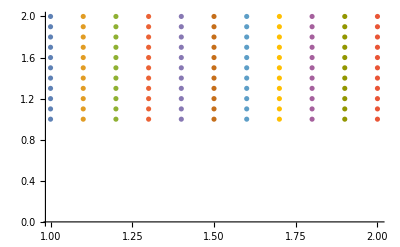

```mathematica
ListPlot[%]
```